Nonlinear Breit–Wheeler pair creation with bremsstrahlung γ rays

T G Blackburn and M Marklund 2018 Plasma Phys. Control. Fusion 60 054009
Notebook: Óscar Amaro, Feb/Apr 2022 @ GoLP-EPP

Physical constants

```mathematica
(*α fine structure constant*)
α = 1/137; (*[#]*)
(*c speed of light in vacuum*)
c = 299792458; (*[m/s]*)
(*m electron mass*)
m = 0.5109989461/1000; (*[GeV]*)
(*ℏ Planck's constant*)
ℏ = 6.626070040*10^-34  /(2π);
(*e electron abs charge*)
e = 1.6021766208*10^-19;
```

Figure 2
P± probability of pair creation
...
Need to multiply probability by ~2500 to reproduce Figure 2 ...

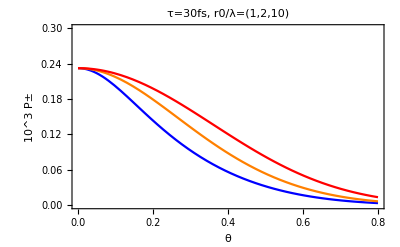

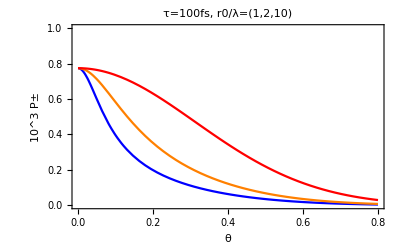

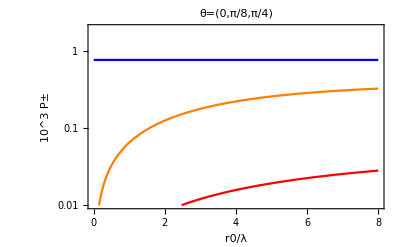

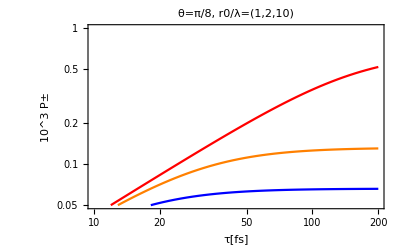

```mathematica
Clear[Ppm,ℛ,neff]
Clear[a0,λ,ω0,ω]

(*fixed parameters*)
a0=30 (*[#]*);
λ=0.8 *10^-6 (*[m]*);
ω0=2π c/λ (*[rad s-1]*);
ω0m=2π c/λ  ℏ / e   10^-9(*[GeV]*);
ω=1000 m (*[GeV]*);
ℛ[x_]:=(0.453 BesselK[1/3,4/(3x)]^2)/(1+0.145x^0.25   Log[1+2.26x]+0.330x)
neff[θ_,r0_,τ_]:=(ω0 τ)/(2π)(1+((c τ)/r0)^2 Tan[θ/2]^2/Log[4])^-0.5
Ppm[θ_,r0_,τ_]:=2.5 10^3  α a0  neff[θ,r0,τ] ℛ[(a0 ω0m ω (1+Cos[θ]))/m^2]

(* (c 30 10^-15)/λ = (ω0 30 10^-15)/(2π) ~ 11.24*)
(* (a0 ω0m ω)/m^2 ~0.091 *)
(*(ω0 30 10^-15)/(2π) ~2.35  10^15*)


Plot[{1000 Ppm[θ,1λ,30 10^-15],1000Ppm[θ,2λ,30*10^-15],1000Ppm[θ,10λ,30*10^-15]},{θ,0,0.8},Axes->False,Frame->True,FrameStyle->Directive[Black,15],PlotStyle->{Blue,Orange,Red},FrameLabel->{"θ","10^3 P±"},PlotLabel->"τ=30fs, r0/λ=(1,2,10)",PlotRange->{0,0.3}]

Plot[{1000Ppm[θ,1λ,100*10^-15],1000Ppm[θ,2λ,100*10^-15],1000Ppm[θ,10λ,100*10^-15]},{θ,0,0.8},Axes->False,Frame->True,FrameStyle->Directive[Black,15],PlotStyle->{Blue,Orange,Red},FrameLabel->{"θ","10^3 P±"},PlotLabel->"τ=100fs, r0/λ=(1,2,10)",PlotRange->{0,1}]

LogPlot[{1000Ppm[0,r0 λ,100*10^-15],1000Ppm[π/8,r0 λ,100*10^-15],1000Ppm[π/4,r0 λ,100*10^-15]},{r0,0,8},Axes->False,Frame->True,FrameStyle->Directive[Black,15],PlotStyle->{Blue,Orange,Red},FrameLabel->{"r0/λ","10^3 P±"},PlotLabel->"θ=(0,π/8,π/4)",PlotRange->{10^-2,2}]

LogLogPlot[{1000Ppm[π/8,1λ,τ 10^-15],1000Ppm[π/8,2λ,τ 10^-15],1000Ppm[π/8,10λ,τ 10^-15]},{τ,10,200},Axes->False,Frame->True,FrameStyle->Directive[Black,15],PlotStyle->{Blue,Orange,Red},FrameLabel->{"τ[fs]","10^3 P±"},PlotLabel->"θ=π/8, r0/λ=(1,2,10)",PlotRange->{0.05,1}]
```

Figure 3
Bremsstrahlung photon generation

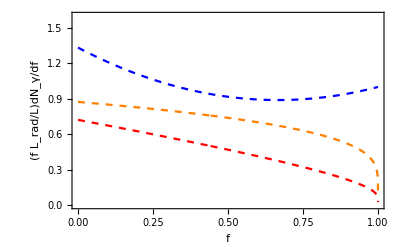

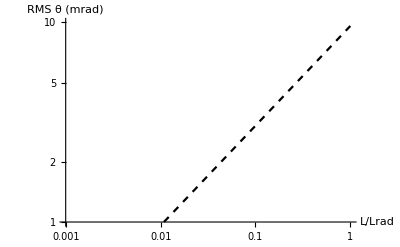

```mathematica
Clear[Lrad,dNγ8,dNγ9,E0, f,l,χe,L]
Lrad=5.6 (*[mm]*);
dNγ8[f_,L_]:=(Lrad f)/L L/(Lrad f)(4/3-4/3 f+f^2) (*(8)*)
dNγ9[f_,L_]:=(Lrad f)/L((1-f)^(4(L/ Lrad)/3)-Exp[-7(L/ Lrad)/9])/(f(7/9+4/3 Log[1-f])) (*(9)*)

Plot[{dNγ8[f,0.2],dNγ9[f,2],dNγ9[f,5]},{f,0,1},PlotRange->{0,1.6},Axes->False,Frame->True,FrameStyle->Directive[Black,15],FrameLabel->{"f","(f L_rad/L)dN_γ/df"},PlotStyle->{Directive[Blue,Dashed],Directive[Orange,Dashed],Directive[Red,Dashed]}]

(* Figure 3 c *)
E0=2000;
LogLogPlot[1000 Sqrt[l]/(E0/19.2),{l,0.001,1},PlotRange->{{0.001,1},{1,10}},PlotStyle->Directive[Dashed,Black],AxesLabel->{"L/Lrad","RMS θ (mrad)"}]
```

Figure 5
Number of positrons

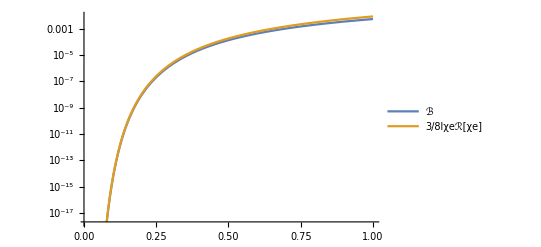

14.9896

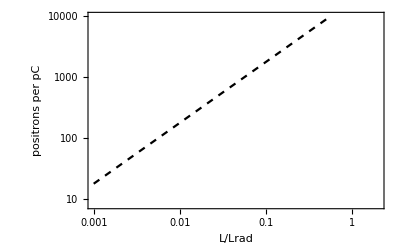

```mathematica
(*prove ℬ~3/8lχeℛ[χe] for χe<<1*)
Clear[ℛ,ℬ,ℬ2,l,χe]
ℛ[x_]:=(0.453 BesselK[1/3,4/(3x)]^2)/(1+0.145x^0.25 Log[1+2.26x]+0.330x)
ℬ[l_,χe_]:=(0.375l χe ℛ[χe])/(1+0.574χe^(2/3))
ℬ2[l_,χe_]:=3/8 l χe ℛ[χe]
l=1;
LogPlot[{ℬ[l,χe]/l,ℬ2[l,χe]/l},{χe,10^-2,1},PlotLegends->{"ℬ","3/8lχeℛ[χe]"}]


Clear[l,a0,τ,λ,E0,ω0,neff,ℬ]
ℬ[l_,χe_]:=(0.375l χe ℛ[χe])/(1+0.574χe^(2/3))
a0=30;
τ=40 (*[fs]*);
λ=0.8 (*[μm]*);
E0=2 (*[GeV]*);
ω0=2π c/(λ 10^-6);
neff=(ω0 τ)/(2π) 10^-15 (*[] should be ~15*)
ω0m=ω0 ℏ/e 10^-9;
χe=E0 a0 ω0m/m^2;

LogLogPlot[α a0 neff ℬ[l,1] (10^6),{l,10^-3,2},Axes->False,Frame->True,PlotStyle->Directive[Black,Dashed],FrameStyle->Directive[Black,15],FrameLabel->{"L/Lrad","positrons per pC"},PlotRange->{8,1 10^4}]
```

Figure 6
Target thickness which maximizes Breit-Wheeler pair creation
...
The equation 15 and expression in-text don’t match Figure 6 but are consistent with each other ...

(7/9 ⅇ^(-7 l/9)+4/3 (1-f)^(4 l/3) Log[1-f])/(f (7/9+4/3 Log[1-f]))

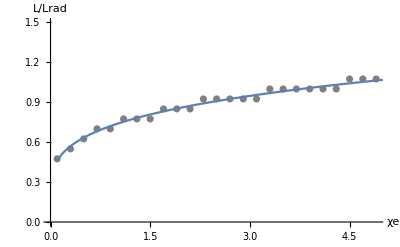

```mathematica
Clear[χe,d2Nγ9,Lrad,l,L,dNγdf,getRootl,lopt2]

(* in-text fitted expression *)
lopt2[χe_]:=0.693 χe^(1/4)+0.0447χe^(-1/5)

(* double differential *)
dNγdf=((1-f)^(4l/3)-Exp[-7l/9])/(f(7/9+4/3 Log[1-f]));
D[dNγdf,l]
Lrad=5.6 (*[mm]*);
d2Nγ9[f_,l_]:=(7/9 ⅇ^(-7 l/9)+4/3 (1-f)^(4 l/3) Log[1-f])/(f (7/9+4/3 Log[1-f]))

(*use (15)*)
(*Get root of equation: do we have to do it numerically or is there an analytic solution?*)
getRootl[χe_]:=Module[{tab,indx},
tab=Table[{l,NIntegrate[ℛ[f χe]d2Nγ9[f  ,l ],{f,0,1}]//Quiet},{l,0.3,1.3,1.3/10}];
indx = Position[Abs[tab[[All,2]] ], Min[ Abs[tab[[All,2]] ] ]][[1,1]];
Return[tab[[All,1]][[indx]]];
]

tab=ParallelTable[{χe,getRoot[χe]},{χe,0.1,5,0.2}];

plt1=ListPlot[tab,PlotStyle->Gray,AxesLabel->{"χe","L/Lrad"},PlotRange->{0,1.5}];
plt2=Plot[{0.693χe^0.25+0.0447χe^-0.2},{χe,0.1,5}];
Show[{plt1,plt2}]
```